### Categorization

Tutorial

HeatTrans Package

HeatTrans`

HeatTrans/tutorial/Validation

### Keywords

Details

# Validation tutorial

This tutorial describes validation of heat transfer model by comparison of FEM solvers from AceFEM and NDSolve.

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

Load the package:

```mathematica
Needs["HeatTrans`"]
```

### Compare solvers from AceFEM and NDSolve

Define 2D region, time and material properties.

```mathematica
region=Disk[{0,0},0.05];
endTime=60;
material=<|"Conductivity"->50,"Density"->7800,"SpecificHeat"->470|>;
```

Prepare ElementMesh object from Disk shape.

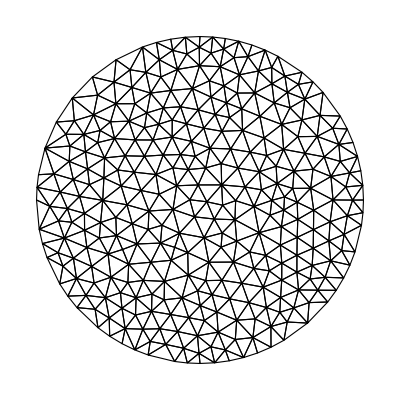

```mathematica
mesh=MakeMesh[region,1];
mesh["Wireframe"]
```

Use HeatTransfer function with different solvers (option Method).

```mathematica
resultAceFEM=HeatTransfer[mesh,endTime,material,Method->"AceFEM"]
```

InterpolatingFunction[…]

```mathematica
resultNDSolve=HeatTransfer[mesh,endTime,material,Method->"NDSolve"]
```

InterpolatingFunction[…]

Curves of temperature versus time, calculated with HeatTransfer and NDSolve, overlap very closely.

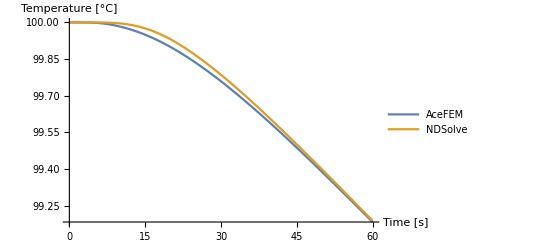

```mathematica
Plot[
{resultAceFEM[t,0,0],resultNDSolve[t,0,0]},
{t,0,endTime},
AxesLabel->{"Time [s]","Temperature [°C]"},
PlotLegends->{"AceFEM","NDSolve"}
]
```

Compare length of time steps for different solutions. NDSolve by default makes more steps.

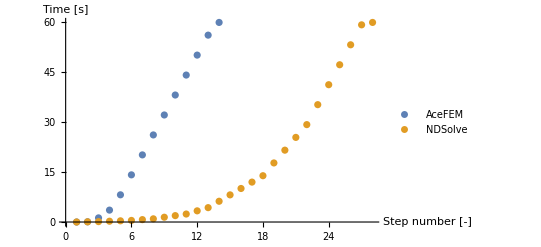

```mathematica
ListPlot[
First/@Through[{resultAceFEM,resultNDSolve}["Coordinates"]],
AxesLabel->{"Step number [-]","Time [s]"},
PlotLegends->{"AceFEM","NDSolve"}
]
```

### Compare solvers with similar time step size

Repeat the same calculation as above, but with fixed maximal time step.

```mathematica
resultAceFEM=HeatTransfer[mesh,endTime,material,Method->"AceFEM",MaxStepSize->1];
resultNDSolve=HeatTransfer[mesh,endTime,material,Method->"NDSolve",MaxStepSize->1];
```

Curves are overlaping completely.

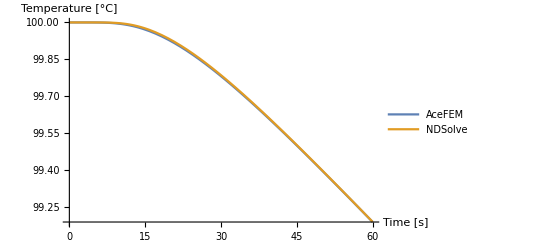

```mathematica
Plot[
{resultAceFEM[t,0,0],resultNDSolve[t,0,0]},
{t,0,endTime},
AxesLabel->{"Time [s]","Temperature [°C]"},
PlotLegends->{"AceFEM","NDSolve"}
]
```

We can see that now both methods use almost the same number of steps.

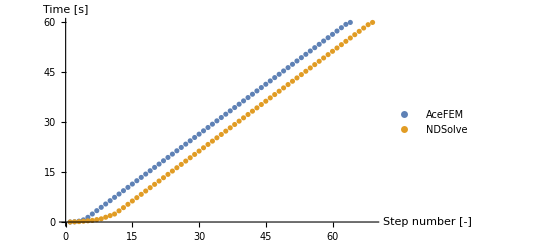

```mathematica
ListPlot[
First/@Through[{resultAceFEM,resultNDSolve}["Coordinates"]],
AxesLabel->{"Step number [-]","Time [s]"},
PlotLegends->{"AceFEM","NDSolve"}
]
```

More About

Related Tutorials

Related Wolfram Education Group Courses